# Stability of hypersurfaces with constant mean curvature trapped between two parallel hyperplanes

This Mathematica notebook includes the computations to generate data and draw figures in the following papers.
[1] M. Koiso and U. Miyamoto, JSIAM Letters 15, pp.9-12 (2023) [arXiv:2306.12211]
[2] M. Koiso and U. Miyamoto, to appear in JJIAM (2023) [arXiv:1905.01705]
where [1] is a letter version of full paper [2]. If one uses or arranges this notebook in your analysis for any publication, he/she has to cite the above papers appropriately. In this notebook, we calculate the mean curvature H, surface area A, and volume V of spheres, cylinders, and unduloids in R^(n+2), and then draw (V, A) diagrams for several n’s. In addition, we draw (s, H’(s)) and (s, V’(s)) diagrams, where s is the parameter characterizing the family of unduloids.

Umpei Miyamoto
Research and Education Center for Comprehensive Science, Akita Prefectural University
Email: umpei@akita-pu.ac.jp
Webpage: http://www.akita-pu.ac.jp/reccs/umiyamoto/
Github: https://github.com/UmpeiMiyamoto/
July 2023

## Preparation

```mathematica
(* copy and paste the path to a directory in your computer, to which the data and figures are exported *)
SetDirectory["path_to_a_directory"];
```

```mathematica
SetOptions[NIntegrate,WorkingPrecision->40,PrecisionGoal->16,AccuracyGoal->16,MinRecursion->3,MaxRecursion->10];

Off[NIntegrate::precw]
dir[1]:=ToString[n]
```

```mathematica
(* normalization *)
L=2;
```

```mathematica
(* volume of a unit n-sphere S^n and a unit (n+1)-volume B^(n+1) *)
sn[nn_]=(2 π^((nn+1)/2))/Gamma[(nn+1)/2]
bn[nn_]=sn[nn]/(nn+1)
```

(2 π^((1+nn)/2))/Gamma[(1+nn)/2]

(2 π^((1+nn)/2))/((1+nn) Gamma[(1+nn)/2])

```mathematica
(* check: sn[1]=2π*1, bn[1]=π*1^2 *)
sn[1]
bn[1]
```

2 π

π

```mathematica
(* (volume of marginally stable cylinder)/(volume of maximum hemisphere) *)
Table[{n,(2(n+2)sn[n])/((n+1)sn[n+1])((√n)/π)^(n+1)},{n,1,11}]//N
```

{{1.,0.151982},{2.,0.154862},{3.,0.173238},{4.,0.213025},{5.,0.284419},{6.,0.407852},{7.,0.622721},{8.,1.00539},{9.,1.7069},{10.,3.03333},{11.,5.62099}}

```mathematica
(* slenderness parameter: See also Appendix of Maeda-Miyamoto 2009  *)
Table[{n,π/(√n)},{n,1,11}]//N
```

{{1.,3.14159},{2.,2.22144},{3.,1.8138},{4.,1.5708},{5.,1.40496},{6.,1.28255},{7.,1.18741},{8.,1.11072},{9.,1.0472},{10.,0.993459},{11.,0.947226}}

```mathematica
(* inverse of slenderness parameter *)
Table[{n,(√n)/π},{n,1,11}]//N
```

{{1.,0.31831},{2.,0.450158},{3.,0.551329},{4.,0.63662},{5.,0.711763},{6.,0.779697},{7.,0.842169},{8.,0.900316},{9.,0.95493},{10.,1.00658},{11.,1.05571}}

```mathematica
(* font size in figures *)
SmallFontSize=30;
LargeFontSize=60;
```

```mathematica
(* length of ticks in the zoom figures *)
TicksLength={0.06,0};
```

```mathematica
(* thickness of lines in figures *)

ThicknessVABall=Thickness[0.008];
ThicknessVACyl=Thickness[0.005];
ThicknessVAUnd=Thickness[0.003];

ThicknessVAZoomUnd=Thickness[0.006];

ThicknessdHds=Thickness[.005];
ThicknessdVds=Thickness[0.005];

ThicknessdHdsZoom=Thickness[.01];
ThicknessdVdsZoom=Thickness[0.01];
```

```mathematica
VARange[nn_]:=Which[
nn==6,{{0.38,1.01},{0.9998,1.0035}},
nn==7,{{0.63,1.0001},{0.99995,1.0015}},
nn==8,{{0.78,1.06},{0.9998,1.00023}},
nn==9,{{0.8,1.7},{0.9994,1.00005}},
nn==10,{{0.78,3.15},{0.99882,1.0002}},
nn==11,{{0.78,5.5},{0.9985,1.0002}}
]
```

```mathematica
VAZoomRange[nn_]:=Which[
nn==6,Automatic,
nn==7,{{0.7353,0.744},{0.999997,1.000002}},
nn==8,{{0.78,0.82},{0.999999995,1.00000001}},
nn==9,{{0.82,0.85},{0.999999999,1.0000000005}},
nn==10,{{0.843,0.86},{0.999999999995,1.00000000001}},
nn==11,Automatic 
]

VAZoomTicks[nn_]:=Which[
nn==6,Automatic,
nn==7,{{0.736,"0.736",TicksLength},{0.74,"0.740",TicksLength},{0.744,"0.744",TicksLength}},
nn==8,{{0.78,"0.78",TicksLength},{0.8,"0.80",TicksLength},{0.82,"0.82",TicksLength}},
nn==9,{{0.82,"0.82",TicksLength},{0.84,"0.84",TicksLength}},
nn==10,{{0.844,"0.844",TicksLength},{0.852,"0.852",TicksLength},{0.86,"0.86",TicksLength}},
nn==11,Automatic 
]
```

```mathematica
dHdsdVdsZoomRange[nn_]:=Which[
nn==6,Automatic,
nn==7,{{0.66,0.69},{-0.005,0.025}},

nn==8,{{0.7652,0.7659},{-0.0005,0.0015}},

nn==9,{{0.80395,0.80399},{-0.00005,0.00015}},
nn==10,{{0.828989,0.828994},{-0.00001,0.00001}},
nn==11,{{0.8474683,0.8474687},{-0.000001,0.000001}}
]

dHdsdVdsZoomTicks[nn_]:=Which[
nn==6,Automatic,
nn==7,{{0.66,"0.660",TicksLength},{0.675,"0.675",TicksLength},{0.69,"0.690",TicksLength}},
nn==8,{{0.7653,"0.7653",TicksLength},{0.7658,"0.7658",TicksLength}},
nn==9,{{0.80395,"0.80395",TicksLength},{0.80399,"0.80399",TicksLength}},
nn==10,{{0.82899,"0.828990",TicksLength},{0.828993,"0.828993",TicksLength}},
nn==11,{{0.8474683,"0.8474683",TicksLength},{0.8474687,"0.8474687",TicksLength}}
]
```

```mathematica
s0FindRoot[nn_]:=s0->s/.Which[
nn==6,FindRoot[s-999==0,{s,999}],
nn==7,FindRoot[dHds==0,{s,0.4}],
nn==8,FindRoot[s-999==0,{s,999}],
nn==9,FindRoot[s-999==0,{s,999}],
nn==10,FindRoot[s-999==0,{s,999}],
nn==11,FindRoot[s-999==0,{s,999}]
]
```

```mathematica
s1FindRoot[nn_]:=s1->s/.Which[
nn==6,FindRoot[s-999==0,{s,999}],
nn==7,FindRoot[dVds==0,{s,0.5}],
nn==8,FindRoot[dVds==0,{s,0.3}],
nn==9,FindRoot[dVds==0,{s,0.1}],
nn==10,FindRoot[s-999==0,{s,999}],
nn==11,FindRoot[s-999==0,{s,999}]
]
```

```mathematica
s2FindRoot[nn_]:=s2->s/.Which[
nn==6,FindRoot[s-999==0,{s,999}],
nn==7,FindRoot[dVds==0,{s,0.67}],
nn==8,FindRoot[dVds==0,{s,0.76}],
nn==9,FindRoot[dVds==0,{s,0.8}],
nn==10,FindRoot[dVds==0,{s,0.82}],
nn==11,FindRoot[dVds==0,{s,0.82}]
]
```

```mathematica
s3FindRoot[nn_]:=s3->s/.Which[
nn==6,FindRoot[s-999==0,{s,999}],
nn==7,FindRoot[dHds==0,{s,0.67}],
nn==8,FindRoot[dHds==0,{s,0.79}],
nn==9,FindRoot[dHds==0,{s,0.79}],
nn==10,FindRoot[dHds==0,{s,0.82}],
nn==11,FindRoot[dHds==0,{s,0.82}]
]
```

```mathematica
n=6;
```

## n=6

### A(V) diagram

```mathematica
(* normalized area and volume of S^(n+1)  *)
ABall=1
VBall=R^(n+2)/(L/2)^(n+2)

(* Normalized area and volume of a cylinser *)
ACyl=(sn[n] r^n L)/(sn[n+1] R^(n+1))/.R->((bn[n] r^(n+1) L)/bn[n+1])^(1/(n+2))
VCyl=(bn[n] r^(n+1)L)/(bn[n+1] (L/2)^(n+2))
```

1

R^8

(7^(7/8) r^6)/(4 (5 π)^(1/8) (r^7)^(7/8))

(256 r^7)/(35 π)

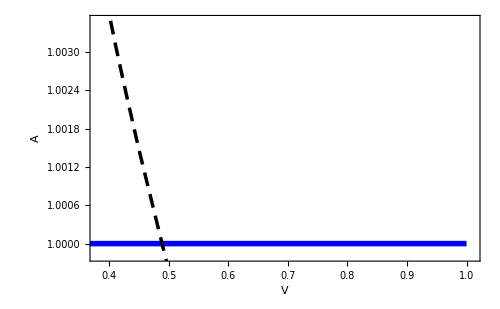

```mathematica
(* A(V) diagrams for the balls and cylinders *)
VABallFig=ParametricPlot[{VBall,ABall},{R,0,L/2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVABall,Blue},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

VACylFig=ParametricPlot[{VCyl,ACyl},{r,0.01,L/2*2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVACyl,Dashing[{0.02,0.012}],Black},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

Show[{VABallFig,VACylFig},PlotRange->VARange[n]]
```

```mathematica
(* Parametric plot of A, V, and H for the unduloids. See also Appendix A of Maeda-Miyamoto JHEP2009 *)
(* wp: dimensionless bulge thickness, wm: dimensionless neck thickness *)
wp=(∑_(m=0)^(n-1) k^m)/(∑_(m=0)^n k^m)
wm=(∑_(m=0)^(n-1) k^(m+1))/(∑_(m=0)^n k^m)
K=((∑_(m=0)^(n-1) k^(m+1))^n)/((∑_(m=0)^n k^m)^(n+1))
```

(1+k+k^2+k^3+k^4+k^5)/(1+k+k^2+k^3+k^4+k^5+k^6)

(k+k^2+k^3+k^4+k^5+k^6)/(1+k+k^2+k^3+k^4+k^5+k^6)

((k+k^2+k^3+k^4+k^5+k^6)^6)/((1+k+k^2+k^3+k^4+k^5+k^6)^7)

```mathematica
(* potential u(w) *)
u[w_]=1-(w^n/(w^(n+1)+K))^2
ψ[hh]=-2/L
ψ[aa]=(2 sn[n] w^n √(1-u[w]))/(-hh)^(n+1)
ψ[vv]=(2 bn[n] w^(n+1))/(-hh)^(n+2)
```

1-w^12/((((k+k^2+k^3+k^4+k^5+k^6)^6)/((1+k+k^2+k^3+k^4+k^5+k^6)^7)+w^7)^2)

-1

-(32 π^3 w^6 √(w^12/((((k+k^2+k^3+k^4+k^5+k^6)^6)/((1+k+k^2+k^3+k^4+k^5+k^6)^7)+w^7)^2)))/(15 hh^7)

(32 π^3 w^7)/(105 hh^8)

```mathematica
gm:=((∑_(l=0)^m k^(l-m+n-1))(∑_(l=0)^n k^l)^(m-n+1))/((∑_(l=0)^(n-1) k^l)^(m-n+2))
g[w_]=∑_(m=0)^(n-1) gm w^m
```

(k^5 (1+k+k^2+k^3+k^4+k^5)^4)/((1+k+k^2+k^3+k^4+k^5+k^6)^5)+((k^4+k^5) (1+k+k^2+k^3+k^4+k^5)^3 w)/((1+k+k^2+k^3+k^4+k^5+k^6)^4)+((k^3+k^4+k^5) (1+k+k^2+k^3+k^4+k^5)^2 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6)^3)+((k^2+k^3+k^4+k^5) (1+k+k^2+k^3+k^4+k^5) w^3)/((1+k+k^2+k^3+k^4+k^5+k^6)^2)+((k+k^2+k^3+k^4+k^5) w^4)/(1+k+k^2+k^3+k^4+k^5+k^6)+w^5

```mathematica
(* Integrands *)
wsubs=w->(wp+wm)/2+(wp-wm)/2 x
integrand[quant_]=((w^(n+1)+K)ψ[quant])/(√((w^(n+1)+w^n+K)(1-x^2)g[w]))
```

w→1/2 ((1+k+k^2+k^3+k^4+k^5)/(1+k+k^2+k^3+k^4+k^5+k^6)+(k+k^2+k^3+k^4+k^5+k^6)/(1+k+k^2+k^3+k^4+k^5+k^6))+1/2 ((1+k+k^2+k^3+k^4+k^5)/(1+k+k^2+k^3+k^4+k^5+k^6)-(k+k^2+k^3+k^4+k^5+k^6)/(1+k+k^2+k^3+k^4+k^5+k^6)) x

((((k+k^2+k^3+k^4+k^5+k^6)^6)/((1+k+k^2+k^3+k^4+k^5+k^6)^7)+w^7) ψ[quant])/(√(((k^5 (1+k+k^2+k^3+k^4+k^5)^4)/((1+k+k^2+k^3+k^4+k^5+k^6)^5)+((k^4+k^5) (1+k+k^2+k^3+k^4+k^5)^3 w)/((1+k+k^2+k^3+k^4+k^5+k^6)^4)+((k^3+k^4+k^5) (1+k+k^2+k^3+k^4+k^5)^2 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6)^3)+((k^2+k^3+k^4+k^5) (1+k+k^2+k^3+k^4+k^5) w^3)/((1+k+k^2+k^3+k^4+k^5+k^6)^2)+((k+k^2+k^3+k^4+k^5) w^4)/(1+k+k^2+k^3+k^4+k^5+k^6)+w^5) (((k+k^2+k^3+k^4+k^5+k^6)^6)/((1+k+k^2+k^3+k^4+k^5+k^6)^7)+w^6+w^7) (1-x^2)))

```mathematica
length=100;
(* s=0:cylinder; s=1:sphere *)
sList=Table[0.0005+(Sin[π/2((i-1)/(length+1))])^((n+2)/n),{i,1,length}]
kList=1-sList;
```

{0.0005,0.00438187,0.0102801,0.0172887,0.0251285,0.0336468,0.0427434,0.0523463,0.0623999,0.0728596,0.0836882,0.0948541,0.10633,0.11809,0.130114,0.142381,0.154872,0.167571,0.180461,0.193527,0.206755,0.22013,0.233641,0.247274,0.261018,0.27486,0.288789,0.302795,0.316866,0.330993,0.345164,0.35937,0.373601,0.387848,0.402101,0.416351,0.430589,0.444806,0.458994,0.473142,0.487244,0.501291,0.515274,0.529186,0.543018,0.556763,0.570413,0.583961,0.597398,0.610717,0.623912,0.636975,0.649899,0.662677,0.675303,0.687769,0.700069,0.712198,0.724147,0.735912,0.747486,0.758863,0.770037,0.781003,0.791755,0.802288,0.812596,0.822674,0.832518,0.842121,0.851479,0.860589,0.869444,0.878041,0.886375,0.894443,0.90224,0.909762,0.917006,0.923969,0.930646,0.937035,0.943132,0.948934,0.954439,0.959644,0.964547,0.969144,0.973434,0.977414,0.981084,0.98444,0.987481,0.990206,0.992614,0.994703,0.996473,0.997922,0.999049,0.999855}

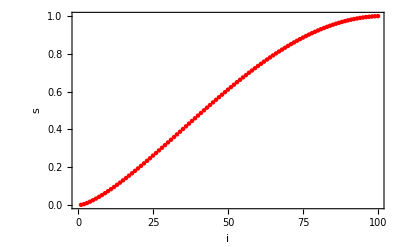

```mathematica
ListPlot[sList,Frame->True,FrameLabel->{"i","s"},BaseStyle->{Large},PlotStyle->{PointSize[.008],Red}]
```

```mathematica
HList=Table[NIntegrate[integrand[hh]/.wsubs/.k->kList[[i]],{x,-1,1}],{i,1,length}];
AList=Table[NIntegrate[integrand[aa]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
VList=Table[NIntegrate[integrand[vv]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
```

```mathematica
(* Tables of (s,H), (s,A), (s,V) *)
sHTable=Thread[{sList,HList}];
sATable=Thread[{sList,AList}];
sVTable=Thread[{sList,VList}];
```

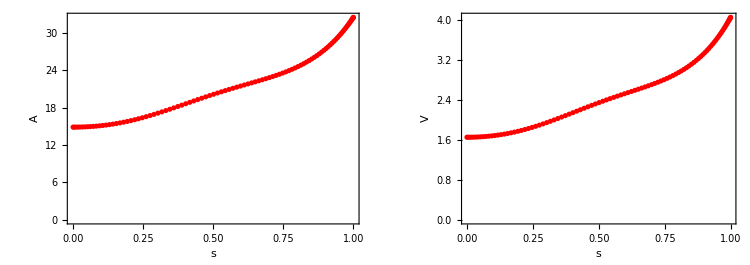

```mathematica
sAFig=ListPlot[sATable,BaseStyle->{Large,Red},FrameLabel->{"s","A"},Frame->True];
sVFig=ListPlot[sVTable,BaseStyle->{Large,Red},FrameLabel->{"s","V"},Frame->True];
GraphicsRow[{sAFig,sVFig},ImageSize->750]
```

```mathematica
(* Normalized area and volume of unduloids *)
ANorm=a/(sn[n+1] R^(n+1))/.R->(v/bn[n+1])^(1/(n+2))
VNorm=v/(bn[n+1] (L/2)^(n+2))
```

(3^(1/8) a)/(4 2^(5/8) √π v^(7/8))

(24 v)/π^4

```mathematica
(* Lists of normalized area, volume, and volume-area *)
ANormList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length,3}];
VNormList=Table[VNorm/.v->VList[[ii]],{ii,1,length,3}];
VNormANormTable=Thread[{VNormList,ANormList}];

(* Full lists of A, V, (V,A) for fine plot *)
ANormFullList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length}];
VNormFullList=Table[VNorm/.v->VList[[ii]],{ii,1,length}];
VNormANormFullTable=Thread[{VNormFullList,ANormFullList}];
```

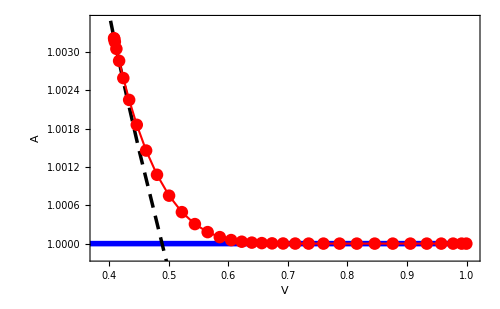

```mathematica
VNormANormFig=ListPlot[VNormANormTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFig=Show[{VABallFig,VACylFig,VNormANormFig},PlotRange->VARange[n]]
```

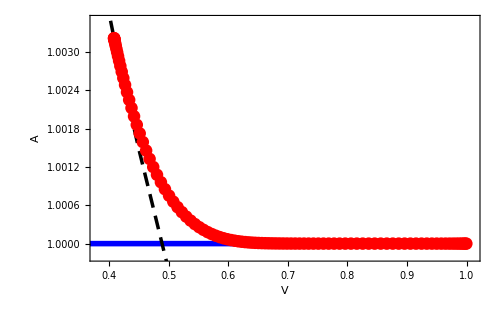

```mathematica
VNormANormFullFig=ListPlot[VNormANormFullTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullFig=Show[{VABallFig,VACylFig,VNormANormFullFig},PlotRange->VARange[n]]
```

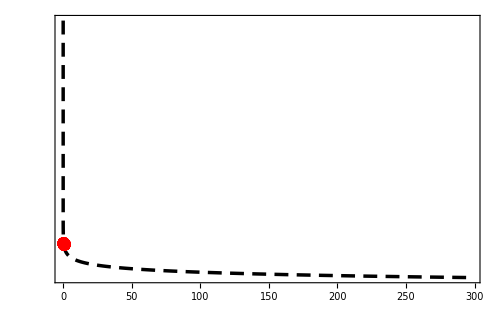

```mathematica
VNormANormFullZoomFig=ListPlot[VNormANormFullTable,Frame->True,BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAZoomUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullZoomFig=Show[{VABallFig,VACylFig,VNormANormFullZoomFig},BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotRange->VAZoomRange[n],FrameTicks->{{None,None},{VAZoomTicks[n],None}},FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"VA.eps",VAFig];
Export["n"<>dir[1]<>"VAZoom.eps",VAFullZoomFig];
Export["n"<>dir[1]<>"VA.dat",VNormANormFullTable];
```

### H’(s) and V’(s) diagrams

```mathematica
(* Make interporation functions of H(s) and V(s) *)
Hs=Interpolation[sHTable,InterpolationOrder->20];
Vs=Interpolation[sVTable,InterpolationOrder->20];
(* Derivatives H'(s) and V'(s) *)
dHds=D[Hs[s],s];
dVds=D[Vs[s],s];
(* Limits of H'(s->1) and V'(s->1) *)
dHdsEnd=Abs[dHds/.s->1]
dVdsEnd=Abs[dVds/.s->1]
```

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

0.297713

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

9.66664

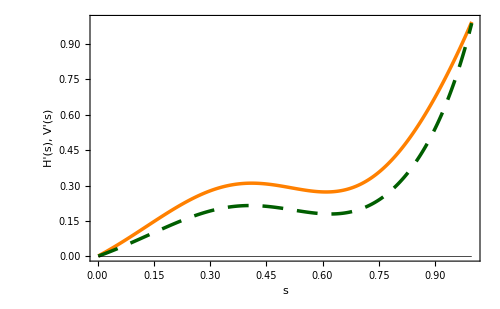

```mathematica
dHdsdVdsFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->{"s","H'(s), V'(s)"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHds,Orange},{ThicknessdVds,Dashing[{0.03,0.02}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->{{0,1},{Automatic,1}},PlotPoints->2000]
```

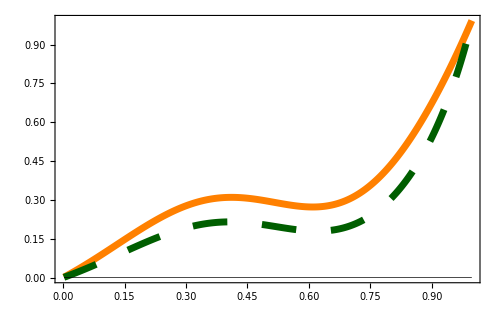

```mathematica
dHdsdVdsZoomFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHdsZoom,Orange},{ThicknessdVdsZoom,Dashing[{0.05,0.05}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->dHdsdVdsZoomRange[n],PlotPoints->2000,FrameTicks->{{None,None},{dHdsdVdsZoomTicks[n],None}},FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"dHdsdVds.eps",dHdsdVdsFig];
Export["n"<>dir[1]<>"dHdsdVdsZoom.eps",dHdsdVdsZoomFig];
```

```mathematica
(* values of Subscript[s, i] (i=0,1,2,3). 999 implies N/A *)
s0FindRoot[n]
s1FindRoot[n]
s2FindRoot[n]
s3FindRoot[n]
```

s0→999.

s1→999.

s2→999.

s3→999.

## n=7

### A(V) diagram

```mathematica
n=n+1
```

7

```mathematica
(* normalized area and volume of S^(n+1)  *)
ABall=1
VBall=R^(n+2)/(L/2)^(n+2)

(* Normalized area and volume of a cylinser *)
ACyl=(sn[n] r^n L)/(sn[n+1] R^(n+1))/.R->((bn[n] r^(n+1) L)/bn[n+1])^(1/(n+2))
VCyl=(bn[n] r^(n+1)L)/(bn[n+1] (L/2)^(n+2))
```

1

R^9

(4 2^(2/9) 35^(1/9) r^7)/(3 3^(7/9) (r^8)^(8/9))

(315 r^8)/128

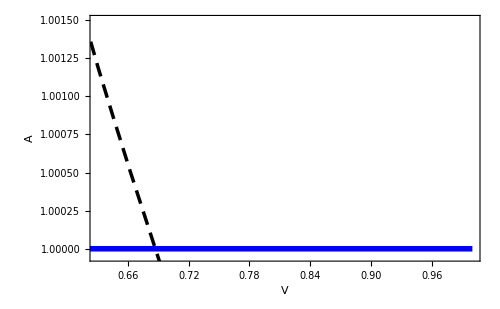

```mathematica
(* A(V) diagrams for the balls and cylinders *)
VABallFig=ParametricPlot[{VBall,ABall},{R,0,L/2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVABall,Blue},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

VACylFig=ParametricPlot[{VCyl,ACyl},{r,0.01,L/2*2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVACyl,Dashing[{0.02,0.012}],Black},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

Show[{VABallFig,VACylFig},PlotRange->VARange[n]]
```

```mathematica
(* Parametric plot of A, V, and H for the unduloids. See Appendix A of Maeda-Miyamoto JHEP2009 *)
(* wp: dimensionless bulge thickness, wm: dimensionless neck thickness *)
wp=(∑_(m=0)^(n-1) k^m)/(∑_(m=0)^n k^m)
wm=(∑_(m=0)^(n-1) k^(m+1))/(∑_(m=0)^n k^m)
K=((∑_(m=0)^(n-1) k^(m+1))^n)/((∑_(m=0)^n k^m)^(n+1))
```

(1+k+k^2+k^3+k^4+k^5+k^6)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)

(k+k^2+k^3+k^4+k^5+k^6+k^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)

((k+k^2+k^3+k^4+k^5+k^6+k^7)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^8)

```mathematica
(* potential u(w) *)
u[w_]=1-(w^n/(w^(n+1)+K))^2
ψ[hh]=-2/L
ψ[aa]=(2 sn[n] w^n √(1-u[w]))/(-hh)^(n+1)
ψ[vv]=(2 bn[n] w^(n+1))/(-hh)^(n+2)
```

1-w^14/((((k+k^2+k^3+k^4+k^5+k^6+k^7)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^8)+w^8)^2)

-1

(2 π^4 w^7 √(w^14/((((k+k^2+k^3+k^4+k^5+k^6+k^7)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^8)+w^8)^2)))/(3 hh^8)

-(π^4 w^8)/(12 hh^9)

```mathematica
gm:=((∑_(l=0)^m k^(l-m+n-1))(∑_(l=0)^n k^l)^(m-n+1))/((∑_(l=0)^(n-1) k^l)^(m-n+2))
g[w_]=∑_(m=0)^(n-1) gm w^m
```

(k^6 (1+k+k^2+k^3+k^4+k^5+k^6)^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^6)+((k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6)^4 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^5)+((k^4+k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6)^3 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^4)+((k^3+k^4+k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6)^2 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^3)+((k^2+k^3+k^4+k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6) w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^2)+((k+k^2+k^3+k^4+k^5+k^6) w^5)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)+w^6

```mathematica
(* Integrands *)
wsubs=w->(wp+wm)/2+(wp-wm)/2 x
integrand[quant_]=((w^(n+1)+K)ψ[quant])/(√((w^(n+1)+w^n+K)(1-x^2)g[w]))
```

w→1/2 ((1+k+k^2+k^3+k^4+k^5+k^6)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)+(k+k^2+k^3+k^4+k^5+k^6+k^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7))+1/2 ((1+k+k^2+k^3+k^4+k^5+k^6)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)-(k+k^2+k^3+k^4+k^5+k^6+k^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)) x

((((k+k^2+k^3+k^4+k^5+k^6+k^7)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^8)+w^8) ψ[quant])/(√(((k^6 (1+k+k^2+k^3+k^4+k^5+k^6)^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^6)+((k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6)^4 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^5)+((k^4+k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6)^3 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^4)+((k^3+k^4+k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6)^2 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^3)+((k^2+k^3+k^4+k^5+k^6) (1+k+k^2+k^3+k^4+k^5+k^6) w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^2)+((k+k^2+k^3+k^4+k^5+k^6) w^5)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7)+w^6) (((k+k^2+k^3+k^4+k^5+k^6+k^7)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7)^8)+w^7+w^8) (1-x^2)))

```mathematica
length=100;
(* s=0:cylinder; s=1:sphere *)
sList=Table[0.0005+(Sin[π/2((i-1)/(length+1))])^((n+2)/n),{i,1,length}]
kList=1-sList;
```

{0.0005,0.00523311,0.0120377,0.0199271,0.0286117,0.0379354,0.0477976,0.0581263,0.0688666,0.0799746,0.091414,0.103154,0.115168,0.127433,0.139926,0.152629,0.165525,0.178596,0.191828,0.205206,0.218717,0.232348,0.246086,0.25992,0.273838,0.28783,0.301884,0.315991,0.33014,0.344323,0.358528,0.372748,0.386973,0.401194,0.415402,0.429589,0.443747,0.457867,0.471942,0.485963,0.499923,0.513814,0.527628,0.541358,0.554998,0.568538,0.581973,0.595296,0.6085,0.621577,0.634523,0.647329,0.659989,0.672498,0.684849,0.697036,0.709053,0.720895,0.732555,0.744028,0.755309,0.766391,0.777271,0.787942,0.7984,0.808639,0.818655,0.828444,0.838,0.84732,0.856398,0.865231,0.873814,0.882144,0.890217,0.898029,0.905577,0.912856,0.919865,0.926599,0.933055,0.93923,0.945123,0.950729,0.956047,0.961074,0.965808,0.970247,0.974388,0.97823,0.98177,0.985009,0.987943,0.990572,0.992895,0.99491,0.996616,0.998014,0.999101,0.999878}

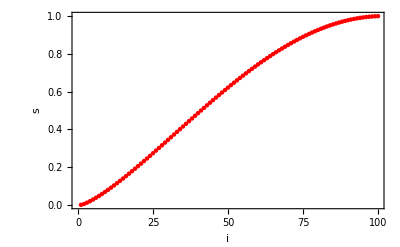

```mathematica
ListPlot[sList,Frame->True,FrameLabel->{"i","s"},BaseStyle->{Large},PlotStyle->{PointSize[.008],Red}]
```

```mathematica
HList=Table[NIntegrate[integrand[hh]/.wsubs/.k->kList[[i]],{x,-1,1}],{i,1,length}];
AList=Table[NIntegrate[integrand[aa]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
VList=Table[NIntegrate[integrand[vv]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
```

```mathematica
(* Tables of (s,H), (s,A), (s,V) *)
sHTable=Thread[{sList,HList}];
sATable=Thread[{sList,AList}];
sVTable=Thread[{sList,VList}];
```

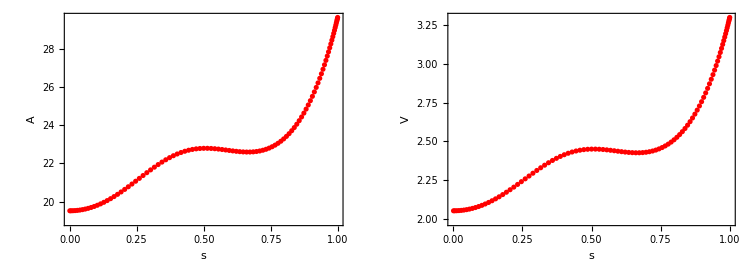

```mathematica
sAFig=ListPlot[sATable,BaseStyle->{Large,Red},FrameLabel->{"s","A"},Frame->True];
sVFig=ListPlot[sVTable,BaseStyle->{Large,Red},FrameLabel->{"s","V"},Frame->True];
GraphicsRow[{sAFig,sVFig},ImageSize->750]
```

```mathematica
(* Normalized area and volume of unduloids *)
ANorm=a/(sn[n+1] R^(n+1))/.R->(v/bn[n+1])^(1/(n+2))
VNorm=v/(bn[n+1] (L/2)^(n+2))
```

(35^(1/9) a)/(3 2^(5/9) 3^(2/3) π^(4/9) v^(8/9))

(945 v)/(32 π^4)

```mathematica
(* Lists of normalized area, volume, and volume-area *)
ANormList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length,3}];
VNormList=Table[VNorm/.v->VList[[ii]],{ii,1,length,3}];
VNormANormTable=Thread[{VNormList,ANormList}];

(* Full lists of A, V, (V,A) for fine plot *)
ANormFullList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length}];
VNormFullList=Table[VNorm/.v->VList[[ii]],{ii,1,length}];
VNormANormFullTable=Thread[{VNormFullList,ANormFullList}];
```

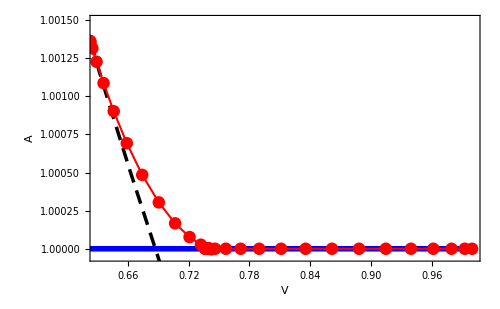

```mathematica
VNormANormFig=ListPlot[VNormANormTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFig=Show[{VABallFig,VACylFig,VNormANormFig},PlotRange->VARange[n]]
```

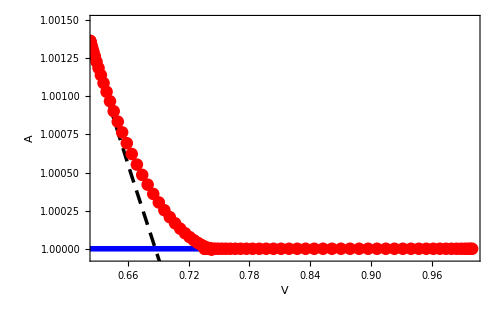

```mathematica
VNormANormFullFig=ListPlot[VNormANormFullTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullFig=Show[{VABallFig,VACylFig,VNormANormFullFig},PlotRange->VARange[n]]
```

```mathematica
VNormANormFullZoomFig=ListPlot[VNormANormFullTable,Frame->True,BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAZoomUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullZoomFig=Show[{VABallFig,VACylFig,VNormANormFullZoomFig},BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotRange->VAZoomRange[n],FrameTicks->{{None,None},{VAZoomTicks[n],None}},FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],FrameTicksStyle->Directive[Thickness[0.004]]];
```

```mathematica
Export["n"<>dir[1]<>"VA.eps",VAFig];
Export["n"<>dir[1]<>"VAZoom.eps",VAFullZoomFig];
Export["n"<>dir[1]<>"VA.dat",VNormANormFullTable];
```

### H’(s) and V’(s) diagrams

```mathematica
(* Make interporation functions of H(s) and V(s) *)
Hs=Interpolation[sHTable,InterpolationOrder->20];
Vs=Interpolation[sVTable,InterpolationOrder->20];
(* Derivatives H'(s) and V'(s) *)
dHds=D[Hs[s],s];
dVds=D[Vs[s],s];
(* Limits of H'(s->1) and V'(s->1) *)
dHdsEnd=Abs[dHds/.s->1]
dVdsEnd=Abs[dVds/.s->1]
```

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

0.250092

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

7.42438

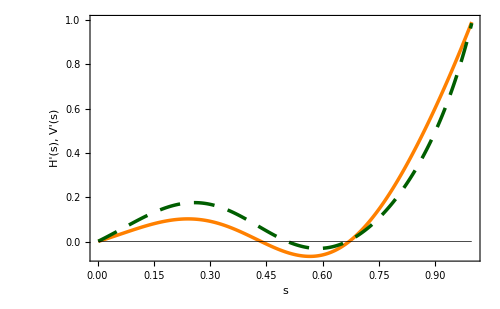

```mathematica
dHdsdVdsFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->{"s","H'(s), V'(s)"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHds,Orange},{ThicknessdVds,Dashing[{0.03,0.02}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->{{0,1},{Automatic,1}},PlotPoints->2000]
```

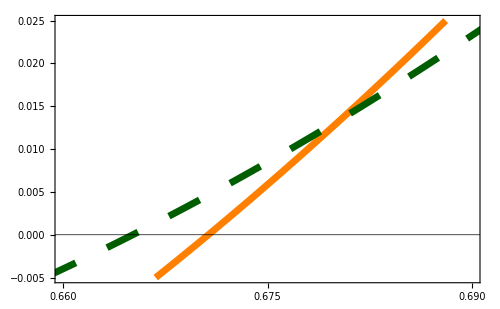

```mathematica
dHdsdVdsZoomFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHdsZoom,Orange},{ThicknessdVdsZoom,Dashing[{0.05,0.05}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->dHdsdVdsZoomRange[n],PlotPoints->2000,FrameTicks->{{None,None},{dHdsdVdsZoomTicks[n],None}},FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"dHdsdVds.eps",dHdsdVdsFig];
Export["n"<>dir[1]<>"dHdsdVdsZoom.eps",dHdsdVdsZoomFig];
```

```mathematica
(* values of Subscript[s, i] (i=0,1,2,3). 999 implies N/A *)
s0FindRoot[n]
s1FindRoot[n]
s2FindRoot[n]
s3FindRoot[n]
```

s0→0.436862

s1→0.507166

s2→0.665112

s3→0.670659

## n=8

### A(V) diagram

```mathematica
n=n+1
```

8

```mathematica
(* normalized area and volume of S^(n+1)  *)
ABall=1
VBall=R^(n+2)/(L/2)^(n+2)

(* Normalized area and volume of a cylinser *)
ACyl=(sn[n] r^n L)/(sn[n+1] R^(n+1))/.R->((bn[n] r^(n+1) L)/bn[n+1])^(1/(n+2))
VCyl=(bn[n] r^(n+1)L)/(bn[n+1] (L/2)^(n+2))
```

1

R^10

(3 3^(4/5) r^8)/(5 (14 π)^(1/10) (r^9)^(9/10))

(512 r^9)/(63 π)

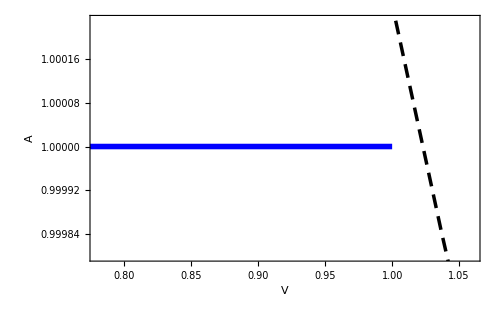

```mathematica
(* A(V) diagrams for the balls and cylinders *)
VABallFig=ParametricPlot[{VBall,ABall},{R,0,L/2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVABall,Blue},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

VACylFig=ParametricPlot[{VCyl,ACyl},{r,0.01,L/2*2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVACyl,Dashing[{0.02,0.012}],Black},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

Show[{VABallFig,VACylFig},PlotRange->VARange[n]]
```

```mathematica
(* Parametric plot of A, V, and H for the unduloids. See Appendix A of Maeda-Miyamoto JHEP2009 *)
(* wp: dimensionless bulge thickness, wm: dimensionless neck thickness *)
wp=(∑_(m=0)^(n-1) k^m)/(∑_(m=0)^n k^m)
wm=(∑_(m=0)^(n-1) k^(m+1))/(∑_(m=0)^n k^m)
K=((∑_(m=0)^(n-1) k^(m+1))^n)/((∑_(m=0)^n k^m)^(n+1))
```

(1+k+k^2+k^3+k^4+k^5+k^6+k^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)

(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)

((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^9)

```mathematica
(* potential u(w) *)
u[w_]=1-(w^n/(w^(n+1)+K))^2
ψ[hh]=-2/L
ψ[aa]=(2 sn[n] w^n √(1-u[w]))/(-hh)^(n+1)
ψ[vv]=(2 bn[n] w^(n+1))/(-hh)^(n+2)
```

1-w^16/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^9)+w^9)^2)

-1

-(64 π^4 w^8 √(w^16/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^9)+w^9)^2)))/(105 hh^9)

(64 π^4 w^9)/(945 hh^10)

```mathematica
gm:=((∑_(l=0)^m k^(l-m+n-1))(∑_(l=0)^n k^l)^(m-n+1))/((∑_(l=0)^(n-1) k^l)^(m-n+2))
g[w_]=∑_(m=0)^(n-1) gm w^m
```

(k^7 (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^7)+((k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^5 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^6)+((k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^4 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^5)+((k^4+k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^3 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^4)+((k^3+k^4+k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^2 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^3)+((k^2+k^3+k^4+k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7) w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7) w^6)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)+w^7

```mathematica
(* Integrands *)
wsubs=w->(wp+wm)/2+(wp-wm)/2 x
integrand[quant_]=((w^(n+1)+K)ψ[quant])/(√((w^(n+1)+w^n+K)(1-x^2)g[w]))
```

w→1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)+(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8))+1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)-(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)) x

((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^9)+w^9) ψ[quant])/(√(((k^7 (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^7)+((k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^5 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^6)+((k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^4 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^5)+((k^4+k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^3 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^4)+((k^3+k^4+k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7)^2 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^3)+((k^2+k^3+k^4+k^5+k^6+k^7) (1+k+k^2+k^3+k^4+k^5+k^6+k^7) w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7) w^6)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)+w^7) (((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^9)+w^8+w^9) (1-x^2)))

```mathematica
length=100;
(* s=0:cylinder; s=1:sphere *)
sList=Table[0.0005+(Sin[π/2((i-1)/(length+1))])^((n+2)/n),{i,1,length}]
kList=1-sList;
```

{0.0005,0.00599195,0.0135601,0.0221747,0.0315437,0.0415122,0.0519813,0.0628804,0.0741562,0.0857663,0.0976757,0.109855,0.122278,0.134923,0.147769,0.160798,0.173994,0.18734,0.200822,0.214428,0.228143,0.241955,0.255854,0.269828,0.283866,0.297958,0.312094,0.326265,0.34046,0.354672,0.368891,0.383108,0.397315,0.411503,0.425666,0.439793,0.453879,0.467915,0.481893,0.495807,0.509649,0.523411,0.537088,0.550671,0.564155,0.577533,0.590797,0.603942,0.616962,0.629849,0.642599,0.655204,0.66766,0.679959,0.692097,0.704068,0.715867,0.727488,0.738925,0.750174,0.76123,0.772087,0.78274,0.793186,0.803419,0.813435,0.823229,0.832798,0.842136,0.85124,0.860105,0.868729,0.877107,0.885235,0.89311,0.900729,0.908088,0.915184,0.922014,0.928576,0.934865,0.940881,0.946619,0.952078,0.957255,0.962148,0.966755,0.971074,0.975104,0.978841,0.982286,0.985436,0.98829,0.990847,0.993105,0.995065,0.996724,0.998083,0.99914,0.999895}

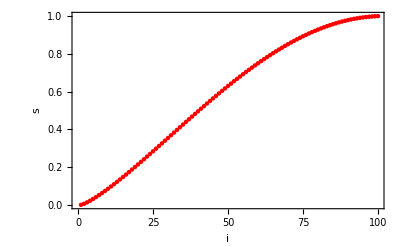

```mathematica
ListPlot[sList,Frame->True,FrameLabel->{"i","s"},BaseStyle->{Large},PlotStyle->{PointSize[.008],Red}]
```

```mathematica
HList=Table[NIntegrate[integrand[hh]/.wsubs/.k->kList[[i]],{x,-1,1}],{i,1,length}];
AList=Table[NIntegrate[integrand[aa]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
VList=Table[NIntegrate[integrand[vv]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
```

```mathematica
(* Tables of (s,H), (s,A), (s,V) *)
sHTable=Thread[{sList,HList}];
sATable=Thread[{sList,AList}];
sVTable=Thread[{sList,VList}];
```

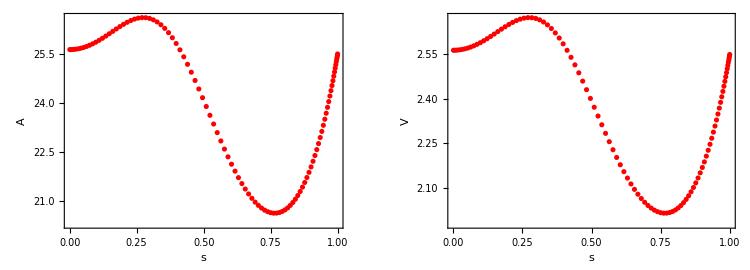

```mathematica
sAFig=ListPlot[sATable,BaseStyle->{Large,Red},FrameLabel->{"s","A"},Frame->True];
sVFig=ListPlot[sVTable,BaseStyle->{Large,Red},FrameLabel->{"s","V"},Frame->True];
GraphicsRow[{sAFig,sVFig},ImageSize->750]
```

```mathematica
(* Normalized area and volume of unduloids *)
ANorm=a/(sn[n+1] R^(n+1))/.R->(v/bn[n+1])^(1/(n+2))
VNorm=v/(bn[n+1] (L/2)^(n+2))
```

(3^(1/10) a)/(2^(7/10) 5^(9/10) √π v^(9/10))

(120 v)/π^5

```mathematica
(* Lists of normalized area, volume, and volume-area *)
ANormList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length,3}];
VNormList=Table[VNorm/.v->VList[[ii]],{ii,1,length,3}];
VNormANormTable=Thread[{VNormList,ANormList}];

(* Full lists of A, V, (V,A) for fine plot *)
ANormFullList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length}];
VNormFullList=Table[VNorm/.v->VList[[ii]],{ii,1,length}];
VNormANormFullTable=Thread[{VNormFullList,ANormFullList}];
```

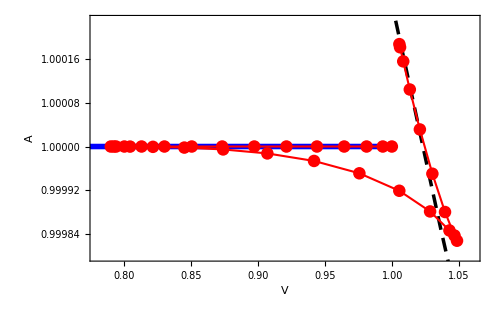

```mathematica
VNormANormFig=ListPlot[VNormANormTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFig=Show[{VABallFig,VACylFig,VNormANormFig},PlotRange->VARange[n]]
```

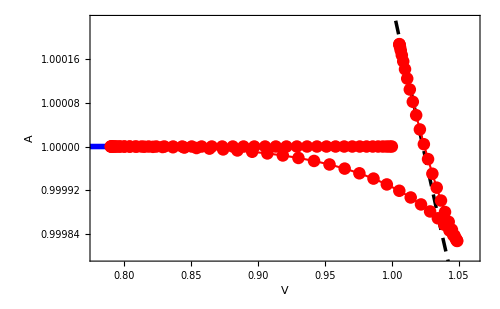

```mathematica
VNormANormFullFig=ListPlot[VNormANormFullTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullFig=Show[{VABallFig,VACylFig,VNormANormFullFig},PlotRange->VARange[n]]
```

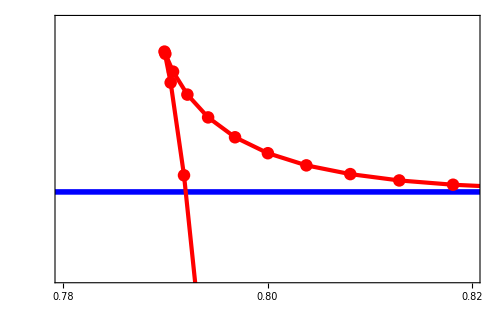

```mathematica
VNormANormFullZoomFig=ListPlot[VNormANormFullTable,Frame->True,BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAZoomUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullZoomFig=Show[{VABallFig,VACylFig,VNormANormFullZoomFig},BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotRange->VAZoomRange[n],FrameTicks->{{None,None},{VAZoomTicks[n],None}},FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"VA.eps",VAFig];
Export["n"<>dir[1]<>"VAZoom.eps",VAFullZoomFig];
Export["n"<>dir[1]<>"VA.dat",VNormANormFullTable];
```

### H’(s) and V’(s) diagrams

```mathematica
(* Make interporation functions of H(s) and V(s) *)
Hs=Interpolation[sHTable,InterpolationOrder->20];
Vs=Interpolation[sVTable,InterpolationOrder->20];
(* Derivatives H'(s) and V'(s) *)
dHds=D[Hs[s],s];
dVds=D[Vs[s],s];
(* Limits of H'(s->1) and V'(s->1) *)
dHdsEnd=Abs[dHds/.s->1]
dVdsEnd=Abs[dVds/.s->1]
```

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

0.215641

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

5.49921

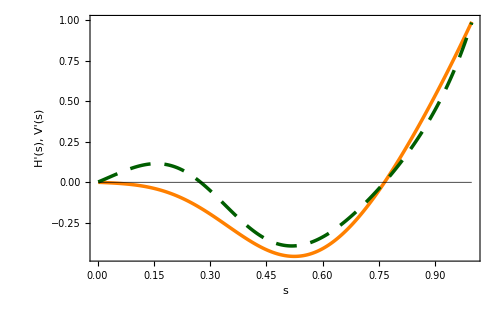

```mathematica
dHdsdVdsFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->{"s","H'(s), V'(s)"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHds,Orange},{ThicknessdVds,Dashing[{0.03,0.02}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->{{0,1},{Automatic,1}},PlotPoints->2000]
```

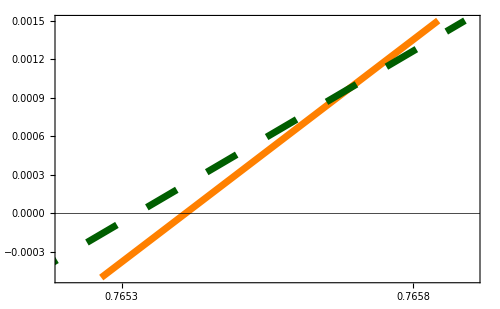

```mathematica
dHdsdVdsZoomFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHdsZoom,Orange},{ThicknessdVdsZoom,Dashing[{0.05,0.05}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->dHdsdVdsZoomRange[n],PlotPoints->2000,FrameTicks->{{None,None},{dHdsdVdsZoomTicks[n],None}},FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"dHdsdVds.eps",dHdsdVdsFig];
Export["n"<>dir[1]<>"dHdsdVdsZoom.eps",dHdsdVdsZoomFig];
```

```mathematica
(* values of Subscript[s, i] (i=0,1,2,3). 999 implies N/A *)
s0FindRoot[n]
s1FindRoot[n]
s2FindRoot[n]
s3FindRoot[n]
```

s0→999.

s1→0.275034

s2→0.765326

s3→0.76541

```mathematica
s1->0.2750339860572028
```

s1→0.275034

```mathematica
s2->0.7653258303711611
```

s2→0.765326

```mathematica
s3->0.7654096268305312
```

s3→0.76541

## n=9

### A(V) diagram

```mathematica
n=n+1
```

9

```mathematica
(* normalized area and volume of S^(n+1)  *)
ABall=1
VBall=R^(n+2)/(L/2)^(n+2)

(* Normalized area and volume of a cylinser *)
ACyl=(sn[n] r^n L)/(sn[n+1] R^(n+1))/.R->((bn[n] r^(n+1) L)/bn[n+1])^(1/(n+2))
VCyl=(bn[n] r^(n+1)L)/(bn[n+1] (L/2)^(n+2))
```

1

R^11

(5 2^(3/11) 3^(2/11) 7^(1/11) r^9)/(11^(10/11) (r^10)^(10/11))

(693 r^10)/256

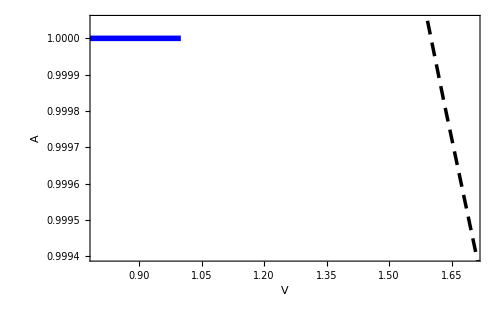

```mathematica
(* A(V) diagrams for the balls and cylinders *)
VABallFig=ParametricPlot[{VBall,ABall},{R,0,L/2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVABall,Blue},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

VACylFig=ParametricPlot[{VCyl,ACyl},{r,0.01,L/2*2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVACyl,Dashing[{0.02,0.012}],Black},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

Show[{VABallFig,VACylFig},PlotRange->VARange[n]]
```

```mathematica
(* Parametric plot of A, V, and H for the unduloids. See Appendix A of Maeda-Miyamoto JHEP2009 *)
(* wp: dimensionless bulge thickness, wm: dimensionless neck thickness *)
wp=(∑_(m=0)^(n-1) k^m)/(∑_(m=0)^n k^m)
wm=(∑_(m=0)^(n-1) k^(m+1))/(∑_(m=0)^n k^m)
K=((∑_(m=0)^(n-1) k^(m+1))^n)/((∑_(m=0)^n k^m)^(n+1))
```

(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)

(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)

((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^10)

```mathematica
(* potential u(w) *)
u[w_]=1-(w^n/(w^(n+1)+K))^2
ψ[hh]=-2/L
ψ[aa]=(2 sn[n] w^n √(1-u[w]))/(-hh)^(n+1)
ψ[vv]=(2 bn[n] w^(n+1))/(-hh)^(n+2)
```

1-w^18/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^10)+w^10)^2)

-1

(π^5 w^9 √(w^18/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^10)+w^10)^2)))/(6 hh^10)

-(π^5 w^10)/(60 hh^11)

```mathematica
gm:=((∑_(l=0)^m k^(l-m+n-1))(∑_(l=0)^n k^l)^(m-n+1))/((∑_(l=0)^(n-1) k^l)^(m-n+2))
g[w_]=∑_(m=0)^(n-1) gm w^m
```

(k^8 (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^8)+((k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^6 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^7)+((k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^5 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^6)+((k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^4 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^5)+((k^4+k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^3 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^4)+((k^3+k^4+k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^2 w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^3)+((k^2+k^3+k^4+k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8) w^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8) w^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)+w^8

```mathematica
(* Integrands *)
wsubs=w->(wp+wm)/2+(wp-wm)/2 x
integrand[quant_]=((w^(n+1)+K)ψ[quant])/(√((w^(n+1)+w^n+K)(1-x^2)g[w]))
```

w→1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)+(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9))+1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)-(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)) x

((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^10)+w^10) ψ[quant])/(√(((k^8 (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^8)+((k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^6 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^7)+((k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^5 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^6)+((k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^4 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^5)+((k^4+k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^3 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^4)+((k^3+k^4+k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8)^2 w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^3)+((k^2+k^3+k^4+k^5+k^6+k^7+k^8) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8) w^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8) w^7)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)+w^8) (((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^10)+w^9+w^10) (1-x^2)))

```mathematica
length=100;
(* s=0:cylinder; s=1:sphere *)
sList=Table[0.0005+(Sin[π/2((i-1)/(length+1))])^((n+2)/n),{i,1,length}]
kList=1-sList;
```

{0.0005,0.0066653,0.0148819,0.0241011,0.0340339,0.0445289,0.0554894,0.0668475,0.0785517,0.0905612,0.102843,0.115368,0.128112,0.141053,0.154173,0.167454,0.18088,0.194436,0.208109,0.221886,0.235754,0.249702,0.263719,0.277795,0.291919,0.306082,0.320274,0.334486,0.34871,0.362936,0.377157,0.391364,0.405549,0.419705,0.433824,0.447897,0.461919,0.475882,0.489778,0.503601,0.517344,0.531,0.544562,0.558025,0.571382,0.584627,0.597753,0.610754,0.623625,0.636359,0.648951,0.661396,0.673687,0.685819,0.697788,0.709587,0.721212,0.732657,0.743918,0.754989,0.765867,0.776546,0.787021,0.797289,0.807345,0.817185,0.826805,0.8362,0.845367,0.854301,0.863,0.871459,0.879676,0.887646,0.895366,0.902834,0.910046,0.916998,0.92369,0.930116,0.936276,0.942166,0.947784,0.953128,0.958195,0.962984,0.967493,0.971719,0.975661,0.979318,0.982687,0.985768,0.98856,0.99106,0.993269,0.995185,0.996808,0.998136,0.99917,0.999909}

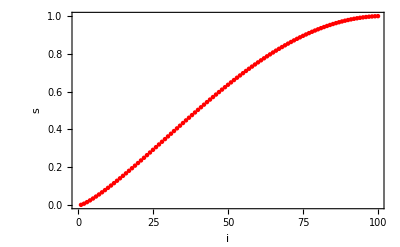

```mathematica
ListPlot[sList,Frame->True,FrameLabel->{"i","s"},BaseStyle->{Large},PlotStyle->{PointSize[.008],Red}]
```

```mathematica
HList=Table[NIntegrate[integrand[hh]/.wsubs/.k->kList[[i]],{x,-1,1}],{i,1,length}];
AList=Table[NIntegrate[integrand[aa]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
VList=Table[NIntegrate[integrand[vv]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
```

```mathematica
(* Tables of (s,H), (s,A), (s,V) *)
sHTable=Thread[{sList,HList}];
sATable=Thread[{sList,AList}];
sVTable=Thread[{sList,VList}];
```

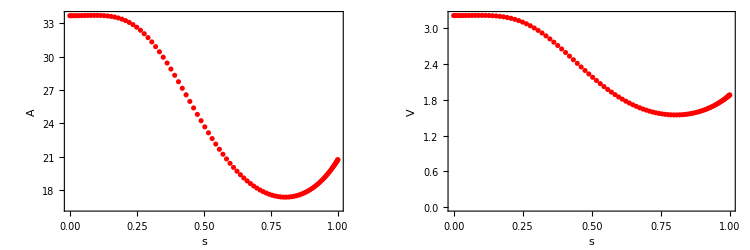

```mathematica
sAFig=ListPlot[sATable,BaseStyle->{Large,Red},FrameLabel->{"s","A"},Frame->True];
sVFig=ListPlot[sVTable,BaseStyle->{Large,Red},FrameLabel->{"s","V"},Frame->True];
GraphicsRow[{sAFig,sVFig},ImageSize->750]
```

```mathematica
(* Normalized area and volume of unduloids *)
ANorm=a/(sn[n+1] R^(n+1))/.R->(v/bn[n+1])^(1/(n+2))
VNorm=v/(bn[n+1] (L/2)^(n+2))
```

(3^(3/11) 35^(1/11) a)/(2^(6/11) 11^(10/11) π^(5/11) v^(10/11))

(10395 v)/(64 π^5)

```mathematica
(* Lists of normalized area, volume, and volume-area *)
ANormList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length,3}];
VNormList=Table[VNorm/.v->VList[[ii]],{ii,1,length,3}];
VNormANormTable=Thread[{VNormList,ANormList}];

(* Full lists of A, V, (V,A) for fine plot *)
ANormFullList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length}];
VNormFullList=Table[VNorm/.v->VList[[ii]],{ii,1,length}];
VNormANormFullTable=Thread[{VNormFullList,ANormFullList}];
```

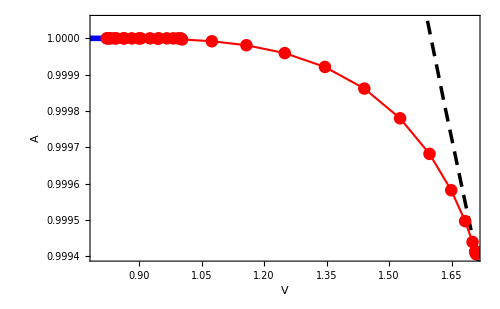

```mathematica
VNormANormFig=ListPlot[VNormANormTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFig=Show[{VABallFig,VACylFig,VNormANormFig},PlotRange->VARange[n]]
```

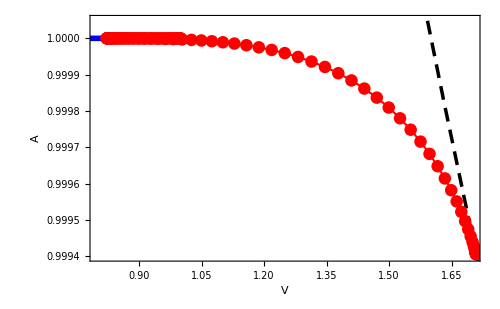

```mathematica
VNormANormFullFig=ListPlot[VNormANormFullTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullFig=Show[{VABallFig,VACylFig,VNormANormFullFig},PlotRange->VARange[n]]
```

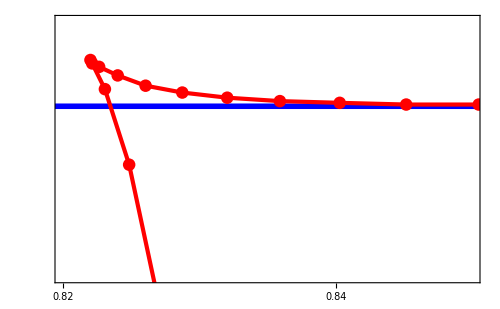

```mathematica
VNormANormFullZoomFig=ListPlot[VNormANormFullTable,Frame->True,BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAZoomUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullZoomFig=Show[{VABallFig,VACylFig,VNormANormFullZoomFig},BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotRange->VAZoomRange[n],FrameTicks->{{None,None},{VAZoomTicks[n],None}},FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"VA.eps",VAFig];
Export["n"<>dir[1]<>"VAZoom.eps",VAFullZoomFig];
Export["n"<>dir[1]<>"VA.dat",VNormANormFullTable];
```

### H’(s) and V’(s) diagrams

```mathematica
(* Make interporation functions of H(s) and V(s) *)
Hs=Interpolation[sHTable,InterpolationOrder->20];
Vs=Interpolation[sVTable,InterpolationOrder->20];
(* Derivatives H'(s) and V'(s) *)
dHds=D[Hs[s],s];
dVds=D[Vs[s],s];
(* Limits of H'(s->1) and V'(s->1) *)
dHdsEnd=Abs[dHds/.s->1]
dVdsEnd=Abs[dVds/.s->1]
```

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

0.189551

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

3.92847

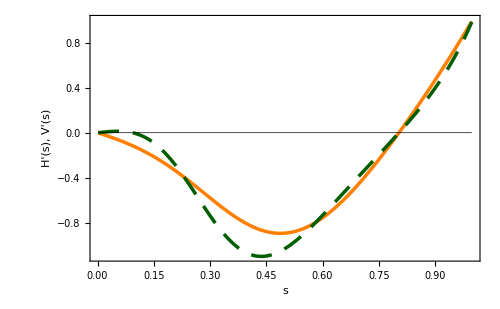

```mathematica
dHdsdVdsFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->{"s","H'(s), V'(s)"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHds,Orange},{ThicknessdVds,Dashing[{0.03,0.02}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->{{0,1},{Automatic,1}},PlotPoints->2000]
```

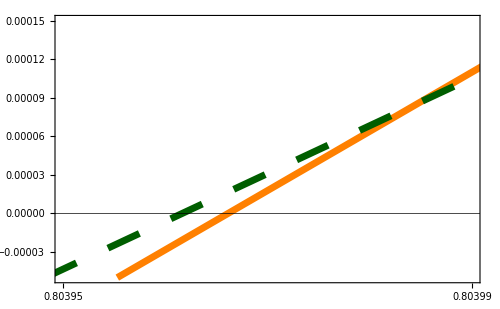

```mathematica
dHdsdVdsZoomFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHdsZoom,Orange},{ThicknessdVdsZoom,Dashing[{0.05,0.05}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->dHdsdVdsZoomRange[n],PlotPoints->2000,FrameTicks->{{None,None},{dHdsdVdsZoomTicks[n],None}},FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"dHdsdVds.eps",dHdsdVdsFig];
Export["n"<>dir[1]<>"dHdsdVdsZoom.eps",dHdsdVdsZoomFig];
```

```mathematica
(* values of Subscript[s, i] (i=0,1,2,3). 999 implies N/A *)
s0FindRoot[n]
s1FindRoot[n]
s2FindRoot[n]
s3FindRoot[n]
```

s0→999.

s1→0.0932708

s2→0.803962

s3→0.803966

```mathematica
s1->0.09327075709166491
```

s1→0.0932708

```mathematica
s2->0.803961707423437
```

s2→0.803962

```mathematica
s3->0.8039661923052377
```

s3→0.803966

## n=10

### A(V) diagram

```mathematica
n=n+1
```

10

```mathematica
(* normalized area and volume of S^(n+1)  *)
ABall=1
VBall=R^(n+2)/(L/2)^(n+2)

(* Normalized area and volume of a cylinser *)
ACyl=(sn[n] r^n L)/(sn[n+1] R^(n+1))/.R->((bn[n] r^(n+1) L)/bn[n+1])^(1/(n+2))
VCyl=(bn[n] r^(n+1)L)/(bn[n+1] (L/2)^(n+2))
```

1

R^12

(11^(11/12) r^10)/(6 (42 π)^(1/12) (r^11)^(11/12))

(2048 r^11)/(231 π)

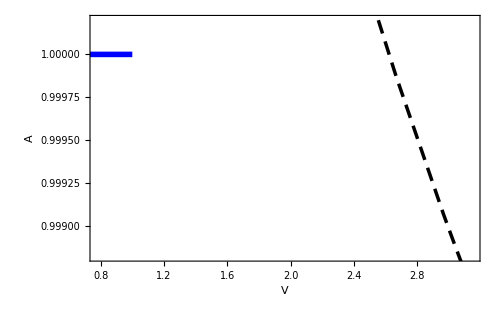

```mathematica
(* A(V) diagrams for the balls and cylinders *)
VABallFig=ParametricPlot[{VBall,ABall},{R,0,L/2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVABall,Blue},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

VACylFig=ParametricPlot[{VCyl,ACyl},{r,0.01,L/2*2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVACyl,Dashing[{0.02,0.012}],Black},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

Show[{VABallFig,VACylFig},PlotRange->VARange[n]]
```

```mathematica
(* Parametric plot of A, V, and H for the unduloids. See Appendix A of Maeda-Miyamoto JHEP2009 *)
(* wp: dimensionless bulge thickness, wm: dimensionless neck thickness *)
wp=(∑_(m=0)^(n-1) k^m)/(∑_(m=0)^n k^m)
wm=(∑_(m=0)^(n-1) k^(m+1))/(∑_(m=0)^n k^m)
K=((∑_(m=0)^(n-1) k^(m+1))^n)/((∑_(m=0)^n k^m)^(n+1))
```

(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)

(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)

((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^10)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^11)

```mathematica
(* potential u(w) *)
u[w_]=1-(w^n/(w^(n+1)+K))^2
ψ[hh]=-2/L
ψ[aa]=(2 sn[n] w^n √(1-u[w]))/(-hh)^(n+1)
ψ[vv]=(2 bn[n] w^(n+1))/(-hh)^(n+2)
```

1-w^20/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^10)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^11)+w^11)^2)

-1

-(128 π^5 w^10 √(w^20/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^10)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^11)+w^11)^2)))/(945 hh^11)

(128 π^5 w^11)/(10395 hh^12)

```mathematica
gm:=((∑_(l=0)^m k^(l-m+n-1))(∑_(l=0)^n k^l)^(m-n+1))/((∑_(l=0)^(n-1) k^l)^(m-n+2))
g[w_]=∑_(m=0)^(n-1) gm w^m
```

(k^9 (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^9)+((k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^7 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^8)+((k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^6 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^7)+((k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^5 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^6)+((k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^4 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^5)+((k^4+k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^3 w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^4)+((k^3+k^4+k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^2 w^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^3)+((k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9) w^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9) w^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)+w^9

```mathematica
(* Integrands *)
wsubs=w->(wp+wm)/2+(wp-wm)/2 x
integrand[quant_]=((w^(n+1)+K)ψ[quant])/(√((w^(n+1)+w^n+K)(1-x^2)g[w]))
```

w→1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)+(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10))+1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)-(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)) x

((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^10)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^11)+w^11) ψ[quant])/(√(((k^9 (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^9)+((k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^7 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^8)+((k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^6 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^7)+((k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^5 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^6)+((k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^4 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^5)+((k^4+k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^3 w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^4)+((k^3+k^4+k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9)^2 w^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^3)+((k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9) w^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9) w^8)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)+w^9) (((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^10)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^11)+w^10+w^11) (1-x^2)))

```mathematica
length=100;
(* s=0:cylinder; s=1:sphere *)
sList=Table[0.0005+(Sin[π/2((i-1)/(length+1))])^((n+2)/n),{i,1,length}]
kList=1-sList;
```

{0.0005,0.00726297,0.016035,0.0257647,0.0361693,0.0471012,0.0584673,0.0702021,0.0822562,0.0945906,0.107173,0.119977,0.132979,0.146158,0.159496,0.172977,0.186586,0.200307,0.214129,0.228039,0.242026,0.256078,0.270185,0.284338,0.298526,0.31274,0.326972,0.341212,0.355453,0.369686,0.383904,0.398097,0.41226,0.426384,0.440463,0.454488,0.468454,0.482353,0.496178,0.509924,0.523583,0.53715,0.550617,0.563979,0.577231,0.590365,0.603376,0.616258,0.629007,0.641615,0.654078,0.666391,0.678548,0.690544,0.702374,0.714033,0.725516,0.736819,0.747936,0.758864,0.769597,0.780131,0.790463,0.800587,0.8105,0.820198,0.829676,0.838931,0.84796,0.856758,0.865323,0.87365,0.881737,0.889579,0.897175,0.904522,0.911615,0.918453,0.925032,0.931351,0.937406,0.943196,0.948717,0.953969,0.958948,0.963654,0.968083,0.972235,0.976107,0.979699,0.983008,0.986034,0.988775,0.991231,0.9934,0.995281,0.996875,0.998179,0.999194,0.99992}

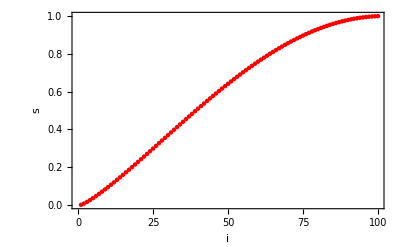

```mathematica
ListPlot[sList,Frame->True,FrameLabel->{"i","s"},BaseStyle->{Large},PlotStyle->{PointSize[.008],Red}]
```

```mathematica
HList=Table[NIntegrate[integrand[hh]/.wsubs/.k->kList[[i]],{x,-1,1}],{i,1,length}];
AList=Table[NIntegrate[integrand[aa]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
VList=Table[NIntegrate[integrand[vv]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
```

```mathematica
(* Tables of (s,H), (s,A), (s,V) *)
sHTable=Thread[{sList,HList}];
sATable=Thread[{sList,AList}];
sVTable=Thread[{sList,VList}];
```

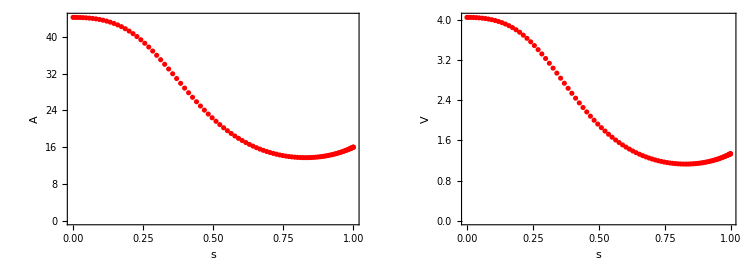

```mathematica
sAFig=ListPlot[sATable,BaseStyle->{Large,Red},FrameLabel->{"s","A"},Frame->True];
sVFig=ListPlot[sVTable,BaseStyle->{Large,Red},FrameLabel->{"s","V"},Frame->True];
GraphicsRow[{sAFig,sVFig},ImageSize->750]
```

```mathematica
(* Normalized area and volume of unduloids *)
ANorm=a/(sn[n+1] R^(n+1))/.R->(v/bn[n+1])^(1/(n+2))
VNorm=v/(bn[n+1] (L/2)^(n+2))
```

(5^(1/12) a)/(2 2^(2/3) 3^(5/6) √π v^(11/12))

(720 v)/π^6

```mathematica
(* Lists of normalized area, volume, and volume-area *)
ANormList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length,3}];
VNormList=Table[VNorm/.v->VList[[ii]],{ii,1,length,3}];
VNormANormTable=Thread[{VNormList,ANormList}];

(* Full lists of A, V, (V,A) for fine plot *)
ANormFullList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length}];
VNormFullList=Table[VNorm/.v->VList[[ii]],{ii,1,length}];
VNormANormFullTable=Thread[{VNormFullList,ANormFullList}];
```

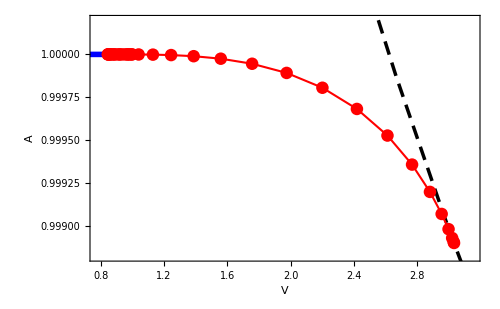

```mathematica
VNormANormFig=ListPlot[VNormANormTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFig=Show[{VABallFig,VACylFig,VNormANormFig},PlotRange->VARange[n]]
```

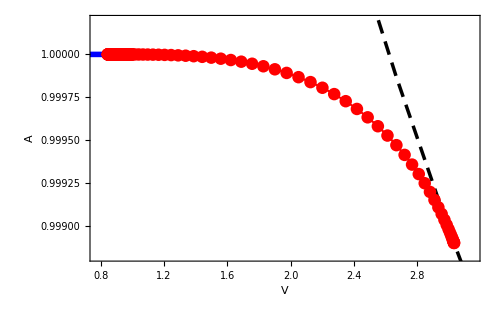

```mathematica
VNormANormFullFig=ListPlot[VNormANormFullTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullFig=Show[{VABallFig,VACylFig,VNormANormFullFig},PlotRange->VARange[n]]
```

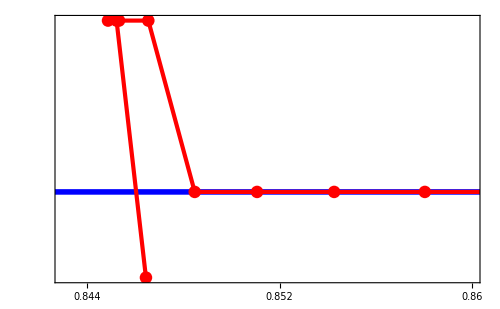

```mathematica
VNormANormFullZoomFig=ListPlot[VNormANormFullTable,Frame->True,BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAZoomUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullZoomFig=Show[{VABallFig,VACylFig,VNormANormFullZoomFig},BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotRange->VAZoomRange[n],FrameTicks->{{None,None},{VAZoomTicks[n],None}},FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"VA.eps",VAFig];
Export["n"<>dir[1]<>"VAZoom.eps",VAFullZoomFig];
Export["n"<>dir[1]<>"VA.dat",VNormANormFullTable];
```

### H’(s) and V’(s) diagrams

```mathematica
(* Make interporation functions of H(s) and V(s) *)
Hs=Interpolation[sHTable,InterpolationOrder->20];
Vs=Interpolation[sVTable,InterpolationOrder->20];
(* Derivatives H'(s) and V'(s) *)
dHds=D[Hs[s],s];
dVds=D[Vs[s],s];
(* Limits of H'(s->1) and V'(s->1) *)
dHdsEnd=Abs[dHds/.s->1]
dVdsEnd=Abs[dVds/.s->1]
```

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

0.169103

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

2.70956

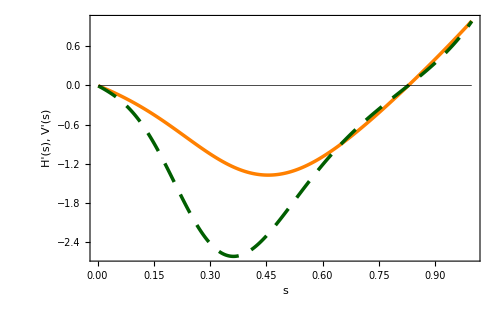

```mathematica
dHdsdVdsFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->{"s","H'(s), V'(s)"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHds,Orange},{ThicknessdVds,Dashing[{0.03,0.02}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->{{0,1},{Automatic,1}},PlotPoints->2000]
```

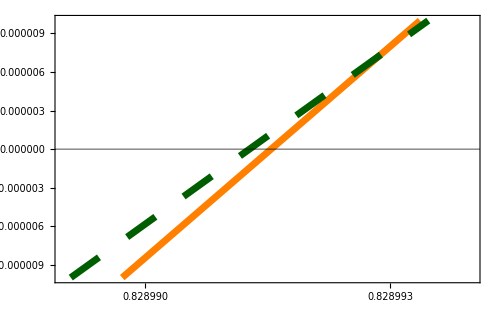

```mathematica
dHdsdVdsZoomFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHdsZoom,Orange},{ThicknessdVdsZoom,Dashing[{0.05,0.05}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->dHdsdVdsZoomRange[n],PlotPoints->2000,FrameTicks->{{None,None},{dHdsdVdsZoomTicks[n],None}},FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"dHdsdVds.eps",dHdsdVdsFig];
Export["n"<>dir[1]<>"dHdsdVdsZoom.eps",dHdsdVdsZoomFig];
```

```mathematica
(* values of Subscript[s, i] (i=0,1,2,3). 999 implies N/A *)
s0FindRoot[n]
s1FindRoot[n]
s2FindRoot[n]
s3FindRoot[n]
```

s0→999.

s1→999.

s2→0.828991

s3→0.828992

```mathematica
s2->0.8289912957656426
```

s2→0.828991

```mathematica
s3->0.8289915603596033
```

s3→0.828992

## n=11

### A(V) diagram

```mathematica
n=n+1
```

11

```mathematica
(* normalized area and volume of S^(n+1)  *)
ABall=1
VBall=R^(n+2)/(L/2)^(n+2)

(* Normalized area and volume of a cylinser *)
ACyl=(sn[n] r^n L)/(sn[n+1] R^(n+1))/.R->((bn[n] r^(n+1) L)/bn[n+1])^(1/(n+2))
VCyl=(bn[n] r^(n+1)L)/(bn[n+1] (L/2)^(n+2))
```

1

R^13

(6 2^(3/13) 231^(1/13) r^11)/(13^(12/13) (r^12)^(12/13))

(3003 r^12)/1024

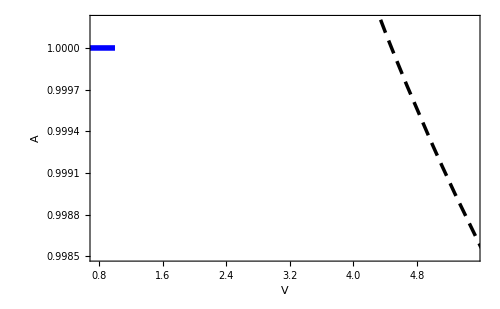

```mathematica
(* A(V) diagrams for the balls and cylinders *)
VABallFig=ParametricPlot[{VBall,ABall},{R,0,L/2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVABall,Blue},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

VACylFig=ParametricPlot[{VCyl,ACyl},{r,0.01,L/2*2},Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{ThicknessVACyl,Dashing[{0.02,0.012}],Black},AspectRatio->1/GoldenRatio,ImageSize->500,PlotRange->Automatic,AxesOrigin->Automatic];

Show[{VABallFig,VACylFig},PlotRange->VARange[n]]
```

```mathematica
(* Parametric plot of A, V, and H for the unduloids. See Appendix A of Maeda-Miyamoto JHEP2009 *)
(* wp: dimensionless bulge thickness, wm: dimensionless neck thickness *)
wp=(∑_(m=0)^(n-1) k^m)/(∑_(m=0)^n k^m)
wm=(∑_(m=0)^(n-1) k^(m+1))/(∑_(m=0)^n k^m)
K=((∑_(m=0)^(n-1) k^(m+1))^n)/((∑_(m=0)^n k^m)^(n+1))
```

(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)

(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)

((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^11)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^12)

```mathematica
(* potential u(w) *)
u[w_]=1-(w^n/(w^(n+1)+K))^2
ψ[hh]=-2/L
ψ[aa]=(2 sn[n] w^n √(1-u[w]))/(-hh)^(n+1)
ψ[vv]=(2 bn[n] w^(n+1))/(-hh)^(n+2)
```

1-w^22/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^11)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^12)+w^12)^2)

-1

(π^6 w^11 √(w^22/((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^11)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^12)+w^12)^2)))/(30 hh^12)

-(π^6 w^12)/(360 hh^13)

```mathematica
gm:=((∑_(l=0)^m k^(l-m+n-1))(∑_(l=0)^n k^l)^(m-n+1))/((∑_(l=0)^(n-1) k^l)^(m-n+2))
g[w_]=∑_(m=0)^(n-1) gm w^m
```

(k^10 (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^10)+((k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^8 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^9)+((k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^7 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^8)+((k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^6 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^7)+((k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^5 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^6)+((k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^4 w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^5)+((k^4+k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^3 w^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^4)+((k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^2 w^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^3)+((k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) w^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) w^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)+w^10

```mathematica
(* Integrands *)
wsubs=w->(wp+wm)/2+(wp-wm)/2 x
integrand[quant_]=((w^(n+1)+K)ψ[quant])/(√((w^(n+1)+w^n+K)(1-x^2)g[w]))
```

w→1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)+(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11))+1/2 ((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)-(k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)) x

((((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^11)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^12)+w^12) ψ[quant])/(√(((k^10 (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^9)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^10)+((k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^8 w)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^9)+((k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^7 w^2)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^8)+((k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^6 w^3)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^7)+((k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^5 w^4)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^6)+((k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^4 w^5)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^5)+((k^4+k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^3 w^6)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^4)+((k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10)^2 w^7)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^3)+((k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) (1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) w^8)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^2)+((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10) w^9)/(1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)+w^10) (((k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^11)/((1+k+k^2+k^3+k^4+k^5+k^6+k^7+k^8+k^9+k^10+k^11)^12)+w^11+w^12) (1-x^2)))

```mathematica
length=100;
(* s=0:cylinder; s=1:sphere *)
sList=Table[0.0005+(Sin[π/2((i-1)/(length+1))])^((n+2)/n),{i,1,length}]
kList=1-sList;
```

{0.0005,0.00779481,0.0170468,0.0272128,0.0380171,0.0493172,0.0610233,0.0730726,0.0854176,0.0980211,0.110852,0.123886,0.137099,0.150472,0.163989,0.177632,0.191388,0.205242,0.219184,0.233201,0.247281,0.261416,0.275593,0.289806,0.304042,0.318296,0.332556,0.346816,0.361068,0.375303,0.389513,0.403693,0.417833,0.431928,0.44597,0.459953,0.473869,0.487713,0.501477,0.515157,0.528744,0.542234,0.555621,0.568898,0.58206,0.595101,0.608016,0.620799,0.633445,0.645948,0.658304,0.670506,0.682551,0.694434,0.706149,0.717691,0.729057,0.740242,0.75124,0.762049,0.772662,0.783078,0.79329,0.803295,0.81309,0.822671,0.832033,0.841173,0.850088,0.858774,0.867228,0.875446,0.883426,0.891165,0.898658,0.905905,0.912901,0.919644,0.926132,0.932362,0.938332,0.944039,0.949482,0.954658,0.959565,0.964202,0.968566,0.972657,0.976472,0.980011,0.983271,0.986252,0.988952,0.991371,0.993507,0.99536,0.99693,0.998214,0.999214,0.999928}

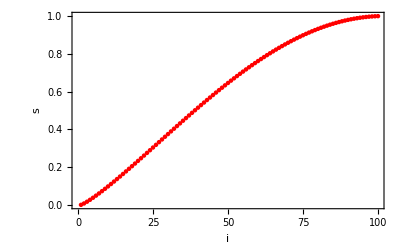

```mathematica
ListPlot[sList,Frame->True,FrameLabel->{"i","s"},BaseStyle->{Large},PlotStyle->{PointSize[.008],Red}]
```

```mathematica
HList=Table[NIntegrate[integrand[hh]/.wsubs/.k->kList[[i]],{x,-1,1}],{i,1,length}];
AList=Table[NIntegrate[integrand[aa]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
VList=Table[NIntegrate[integrand[vv]/.wsubs/.k->kList[[i]]/.hh->HList[[i]],{x,-1,1}],{i,1,length}];
```

```mathematica
(* Tables of (s,H), (s,A), (s,V) *)
sHTable=Thread[{sList,HList}];
sATable=Thread[{sList,AList}];
sVTable=Thread[{sList,VList}];
```

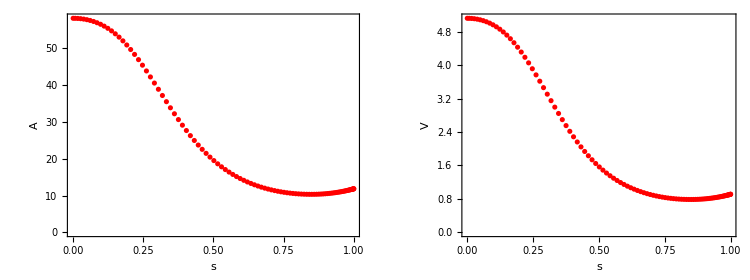

```mathematica
sAFig=ListPlot[sATable,BaseStyle->{Large,Red},FrameLabel->{"s","A"},Frame->True];
sVFig=ListPlot[sVTable,BaseStyle->{Large,Red},FrameLabel->{"s","V"},Frame->True];
GraphicsRow[{sAFig,sVFig},ImageSize->750]
```

```mathematica
(* Normalized area and volume of unduloids *)
ANorm=a/(sn[n+1] R^(n+1))/.R->(v/bn[n+1])^(1/(n+2))
VNorm=v/(bn[n+1] (L/2)^(n+2))
```

(3^(3/13) 385^(1/13) a)/(2^(7/13) 13^(12/13) π^(6/13) v^(12/13))

(135135 v)/(128 π^6)

```mathematica
(* Lists of normalized area, volume, and volume-area *)
ANormList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length,3}];
VNormList=Table[VNorm/.v->VList[[ii]],{ii,1,length,3}];
VNormANormTable=Thread[{VNormList,ANormList}];

(* Full lists of A, V, (V,A) for fine plot *)
ANormFullList=Table[ANorm/.a->AList[[ii]]/.v->VList[[ii]],{ii,1,length}];
VNormFullList=Table[VNorm/.v->VList[[ii]],{ii,1,length}];
VNormANormFullTable=Thread[{VNormFullList,ANormFullList}];
```

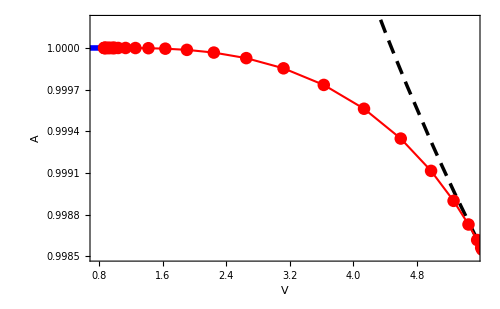

```mathematica
VNormANormFig=ListPlot[VNormANormTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFig=Show[{VABallFig,VACylFig,VNormANormFig},PlotRange->VARange[n]]
```

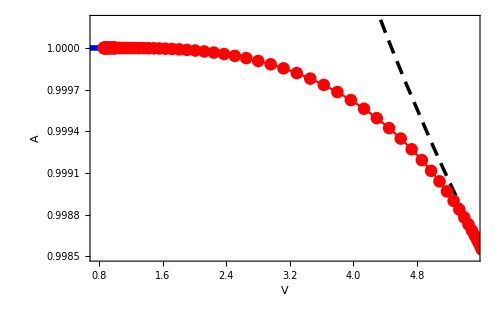

```mathematica
VNormANormFullFig=ListPlot[VNormANormFullTable,Frame->True,FrameLabel->{"V","A"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullFig=Show[{VABallFig,VACylFig,VNormANormFullFig},PlotRange->VARange[n]]
```

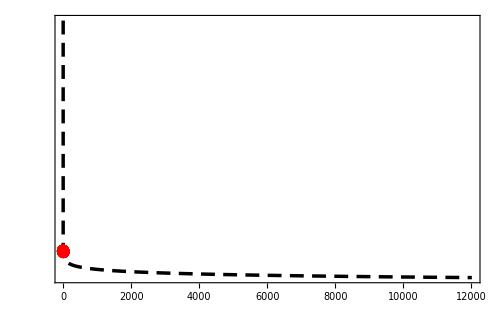

```mathematica
VNormANormFullZoomFig=ListPlot[VNormANormFullTable,Frame->True,BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{PointSize[.018],Red,ThicknessVAZoomUnd},ImageSize->500,AspectRatio->1/GoldenRatio,Joined->True,Mesh->All];

VAFullZoomFig=Show[{VABallFig,VACylFig,VNormANormFullZoomFig},BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotRange->VAZoomRange[n],FrameTicks->{{None,None},{VAZoomTicks[n],None}},FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"VA.eps",VAFig];
Export["n"<>dir[1]<>"VAZoom.eps",VAFullZoomFig];
Export["n"<>dir[1]<>"VA.dat",VNormANormFullTable];
```

### H’(s) and V’(s) diagrams

```mathematica
(* Make interporation functions of H(s) and V(s) *)
Hs=Interpolation[sHTable,InterpolationOrder->20];
Vs=Interpolation[sVTable,InterpolationOrder->20];
(* Derivatives H'(s) and V'(s) *)
dHds=D[Hs[s],s];
dVds=D[Vs[s],s];
(* Limits of H'(s->1) and V'(s->1) *)
dHdsEnd=Abs[dHds/.s->1]
dVdsEnd=Abs[dVds/.s->1]
```

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

0.152642

InterpolatingFunction::dmval: 入力値{1}は補間関数のデータ範囲外です．外挿が使用されます．

1.80701

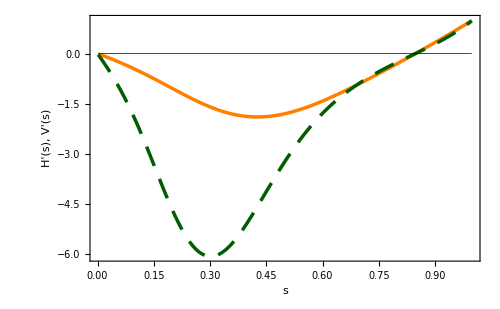

```mathematica
dHdsdVdsFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->{"s","H'(s), V'(s)"},BaseStyle->{FontSize->SmallFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHds,Orange},{ThicknessdVds,Dashing[{0.03,0.02}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->{{0,1},{Automatic,1}},PlotPoints->2000]
```

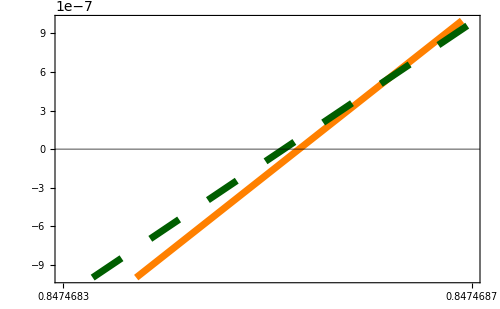

```mathematica
dHdsdVdsZoomFig=Plot[{dHds/dHdsEnd,dVds/dVdsEnd,0},{s,0.002,0.998},Frame->True,FrameLabel->None,FrameStyle->Directive[Thickness[0.004]],BaseStyle->{FontSize->LargeFontSize,FontFamily->Times},PlotStyle->{{ThicknessdHdsZoom,Orange},{ThicknessdVdsZoom,Dashing[{0.05,0.05}],RGBColor[0,0.37,0]},{Thickness[.001],Black}},ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->dHdsdVdsZoomRange[n],PlotPoints->2000,FrameTicks->{{None,None},{dHdsdVdsZoomTicks[n],None}},FrameTicksStyle->Directive[Thickness[0.004]]]
```

```mathematica
Export["n"<>dir[1]<>"dHdsdVds.eps",dHdsdVdsFig];
Export["n"<>dir[1]<>"dHdsdVdsZoom.eps",dHdsdVdsZoomFig];
```

```mathematica
(* values of Subscript[s, i] (i=0,1,2,3). 999 implies N/A *)
s0FindRoot[n]
s1FindRoot[n]
s2FindRoot[n]
s3FindRoot[n]
```

s0→999.

s1→999.

s2→0.847469

s3→0.847469

```mathematica
s2->0.8474685174960644
```

s2→0.847469

```mathematica
s3->0.8474685325629033
```

s3→0.847469